(ⅇ^(-x^2/16) Cos[π x])/(√(1+ⅇ^(-8 π^2)) (2 π)^(1/4))

((ⅇ^(-4 (p-π)^2)+ⅇ^(-4 (p+π)^2)) (2/π)^(1/4))/(√(1+ⅇ^(-8 π^2)))

√((4-(64 π^2)/(1+ⅇ^(8 π^2))) (1/16+(1-1/(1+ⅇ^(8 π^2))) π^2))

6.30305

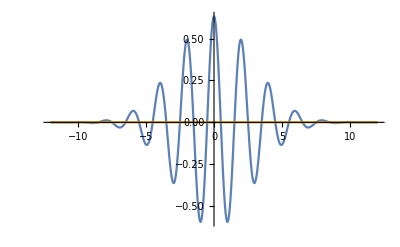

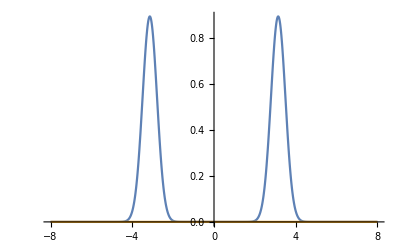

```mathematica
ћ=1;
ψ=Exp[-(x/4)^2]*Cos[π x];
norm[y_]:=y/Sqrt[Integrate[Conjugate[y]y,{x,-Infinity,Infinity}]]
ψ1=norm[ψ]
ϕ=InverseFourierCosTransform[ψ1,x,p]
ex[y_,t_,d_]:=Integrate[Conjugate[y]*t*y,{d,-Infinity,Infinity}]
n=Sqrt[ex[ψ1,x^2,x]-ex[ψ1,x,x]^2]*Sqrt[ex[ϕ,p^2,p]-ex[ϕ,p,p]^2]
N[n]
Plot[{Re[ψ1],Im[ψ1]},{x,-12,12},PlotRange->All,PlotPoints->150]
Plot[{Re[ϕ],Im[ϕ]},{p,-8,8},PlotRange->All,PlotPoints->150]
```